# Useful functions

```mathematica
colorlist = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
makeSystem[var_, vart_, sys_]:=
(* 
Input:
var: variables in an ode system (form: {var1, var2});
vart: variables in the ode system under the form of functions of time (form: {var1[t], var2[t]};
sys: the ode system (form: dvar1dt = a var1 + b var2, dvar2dt = x var2 - y var2 var3);
Output:
The system that can be input for function NDSolve
*)
 Module[{v, vt, S, St, Sf},
v = var;
vt = vart;
S = sys;
(St = S/.Thread[v-> vt]; Sf = Thread[D[vt, t] == St])]
```

```mathematica
FollowRoot[system_,commonpars_,followPar_,range_,variables_, initialEq_]:=Module[{sys,cpar,fp, r,v,en, ieq, eq, pars, results},sys=system;
cpar=commonpars;
fp=followPar;r = range;v=variables;
ieq = initialEq;
results={};
Do[eq=ieq;
pars = Join[cpar, {fp-> i}];
ieq = Check[FindRoot[Thread[sys == ConstantArray[0, Length[v]]]/.pars,Thread[{v, v/.ieq, 0, Infinity}], MaxIterations->1000], Thread[v->-1]];
If[AllTrue[v/.ieq, #==-1&], Break[]];
results = AppendTo[results, ieq], {i, range}];
results];
```

```mathematica
FollowRootTwoParameters[system_,commonpars_,followPar1_,range1_,followPar2_, range2_,variables_, initialEq_, minEqlimit_, maxiteration_:1000, precisionGoal_:MachinePrecision]:=Module[{sys,cpar,fp1, r1, fp2, r2,v,en, ieq,mineqlim,maxiter,precgoal, pars, results},sys=system;
cpar=commonpars;
fp1=followPar1;
r1 = range1;
fp2 = followPar2;
r2 = range2;
v=variables;
ieq = initialEq;
mineqlim = minEqlimit;
maxiter = maxiteration;
precgoal = precisionGoal;
results={};
Do[pars = Join[cpar, {fp1-> i, fp2-> j}];
ieq = Check[FindRoot[Thread[sys == ConstantArray[0, Length[v]]]/.pars,Thread[{v, v/.ieq, minEqlimit, Infinity}], MaxIterations->maxiter, PrecisionGoal->precgoal], Thread[v-> -1]];
If[AllTrue[v/.ieq, # == -1&], Break[]];
results = AppendTo[results, ieq], {i, range1}, {j, range2}];
results];
```

```mathematica
FollowNSolveTwoParameters[system_,commonpars_,followPar1_,range1_,followPar2_, range2_,variables_]:=Module[{vars, sys,cpar,fp1, r1, fp2, r2,v,en,  eqAll, eq, pars, results, parpair},
vars = variables;
sys=system;
cpar=commonpars;
fp1=followPar1;
r1 = range1;
fp2 = followPar2;
r2 = range2;
v=variables;
results={};
parpair = {};
Do[eqAll= NSolve[Thread[(sys/.cpar/.{fp1-> i, fp2-> j})==0], vars, Reals];
eq = Select[eqAll,And@@Thread[(vars/.# )> 0]&];
If[eq != {}, 
results = AppendTo[results, eq[[1]]];
parpair = AppendTo[parpair, {i, j}];
];
, {i, range1}, {j, range2}];
{parpair, results}];
```

```mathematica
NSolveCodim2Positive[system_, commonpars_, bifurpar1_, bifurpar2_,bfparsName_, variables_]:=
(*Find only positive solution varying two parameters, using NSolve (To be used in Parallele Table to follow the positive equilibrium);
----
Input:
system: the odes to be solved (form: dXdt = A * X, where X is the vector of variables and A is the characteristic matrix);
commonpars: list of the value of fixed parameters (form: {p1 -> 4, p2 -> 2, ..., pn -> 43});
bifurpar1: the value of the bifurcation parameter 1 (form: {pb1 -> 3.4});
bifurpar2: the value of the bifurcation parameter 2 (form: {pb2 -> 1.2});
bfparsName: symbol of the two bifurcation parameter (form: pb1pb2);
variables: list of the variables to be solved (form: {v1, v2, v3});
----
Output:
a list of the values of the two bifurcation parameters and its corresponding positive equilibrium
(form: {pb1pb2 -> {2, 2}, v1-> 4, v2-> 3, v3-> 4.5}}
*)
Module[
{sys, cpar,bfpar1, bfpar2,  vars, bfpName,parspairVal, eqAll, eqpos},
sys = system;
cpar = commonpars;
bfpar1 = bifurpar1;
bfpar2 = bifurpar2;
bfpName = bfparsName;
vars = variables;
eqAll = NSolve[Thread[(sys/.cpar/.bfpar1/. bfpar2)==0], vars, Reals];
eqpos = Select[eqAll,And@@Thread[(vars/.# )> 0]&];
parspairVal = {bfpar1[[1]][[2]], bfpar2[[1]][[2]]};
If[eqpos != {}, Join[{bfpName -> parspairVal}, eqpos[[1]]] , Unevaluated@Sequence[]]
]
```

```mathematica
SingleStableColor[jacobmatrix_, parcommon_, parsfollow_, equilibrium_]:=Module[{jmat, pc, pf, r,eq, eiv, anyZero, anyPos, allNeg, ps},
jmat = jacobmatrix;
pc = parcommon;
pf = parsfollow;
eq = equilibrium;
eiv = Eigenvalues[jmat/.pc/.pf/.eq];
anyZero = AnyTrue[Thread[-10^-10<=Re[eiv]<=10^-10], TrueQ];
anyPos = AnyTrue[Thread[Re[eiv]>10^-10], TrueQ];
allNeg = AllTrue[Thread[Re[eiv]<-10^-10], TrueQ];
Which[anyZero, colorlist[[2]],anyPos, colorlist[[1]], allNeg, colorlist[[1]]]]
```

```mathematica
SingleStableMark[jacobmatrix_, parcommon_, parsfollow_, equilibrium_]:=
(* Input:
jacobmatrix: jacobian matrix of the system (form: {{a, b}, {c, d}});
parcommon: values of fixed parameters (form: {p1 -> 2, p2-> 3};
parsfollow: bifurcation parameter which could be one or two parameters(form: {p4 -> 3.4} for one parameter, {p2 -> 1, p4 -> 4} for two parameters);
equilibrium: values of equilibrium (form: {var1 -> 4.5, var2 -> 44};
Output:
 symbol "*" if the equilibrium is unstable, symbol "." if the equilibrium is stable
*)
Module[{jmat, pc, pf, r,eq, eiv, anyZero, anyPos, allNeg, ps},
jmat = jacobmatrix;
pc = parcommon;
pf = parsfollow;
eq = equilibrium;
eiv = Eigenvalues[jmat/.pc/.pf/.eq];
anyZero = AnyTrue[Thread[-10^-10<=Re[eiv]<=10^-10], TrueQ];
anyPos = AnyTrue[Thread[Re[eiv]>10^-10], TrueQ];
allNeg = AllTrue[Thread[Re[eiv]<-10^-10], TrueQ];
Which[anyZero, "*",anyPos, "*", allNeg, "."]]
```

```mathematica
ListStableMark[jacobmatrix_, parcommon_, parfollow_, range_,equiList_]:=
(* Input:
jacobmatrix: jacobian matrix of the system (form: {{a, b}, {c, d}});
parcommon: values of fixed parameters (form: {p1 -> 2, p2-> 3};
parfollow: bifurcation parameter (form: symbol of the bifurcation parameter);
range: values of the bifurcation parameter (form: {0.1, 0.2});
equiList: list of values of equilibrium corresponds with different values of bifurcation parameter (form: {{var1 -> 4.5, var2 -> 44}, {var1 -> 4.6, var2-> 45}};
Output:
 a list of symbols that correspond to the stability of the equilibrium, symbol "*" if the equilibrium is unstable, symbol "." if the equilibrium is stable
(form: {*,*,.,.})*)

Module[{jmat, pc, pf, r,eql, eiv, ps},
jmat = jacobmatrix;
pc = parcommon;
pf = parfollow;
r=range;
eql = equiList;
MapThread[SingleStableMark,{ConstantArray[jmat, Length[eql]], ConstantArray[pc, Length[eql]],Thread[pf->r], eql}]]
```

```mathematica
ListStableMarkTwoParameters[jacobmatrix_, parcommon_, parfollow1_, range1_,parfollow2_, range2_, equiList_, useColor_]:=
(* Input:
jacobmatrix: jacobian matrix of the system (form: {{a, b}, {c, d}});
parcommon: values of fixed parameters (form: {p1 -> 2, p2-> 3};
parfollow1: bifurcation parameter 1 (form: symbol of the bifurcation parameter);
range1: values of the bifurcation parameter 1 (form: {0.1, 0.2});
parfollow2: bifurcation parameter 2 (form: similar to parfollow1);
range2: values of the bifurcation parameter 2 (form: similar to range1);
equiList: list of values of equilibrium corresponds with different values of bifurcation parameter (form: {{var1 -> 4.5, var2 -> 44}, {var1 -> 4.6, var2-> 45}};
Output: 
a list of symbols that correspond to the stability of the equilibrium, symbol "*" if the equilibrium is unstable, symbol "." if the equilibrium is stable
(form: {*,*,.,.})*)

Module[{jmat, pc, pf1, r1,pf2, r2,eql, eiv, listpairParameters, marklist, usecor},
jmat = jacobmatrix;
pc = parcommon;
pf1 = parfollow1;
r1=range1;
pf2 = parfollow2;
r2 = range2;
eql = equiList;
usecor = useColor;
listpairParameters = {};
Do[AppendTo[listpairParameters, {pf1 -> i, pf2 -> j }], {i, r1}, {j, r2}];
If[usecor,marklist = MapThread[SingleStableColor,{ConstantArray[jmat, Length[eql]], ConstantArray[pc, Length[eql]],listpairParameters, eql}],
marklist = MapThread[SingleStableMark,{ConstantArray[jmat, Length[eql]], ConstantArray[pc, Length[eql]],listpairParameters, eql}]];
{{pf1, pf2}/.listpairParameters, marklist}]
```

# Single infection

## Ecological dynamics of a resident

```mathematica
dIsdt = R[Iw, Is]- d Is- Π0[Ds, Dw] Is  - γw W Is ;(*Susceptible intermediate*)
dIwdt =  γw W Is  - (d + α)Iw - Π1[Ds, Dw, βw]Iw; (*Infected intermediate*)
dDsdt =B[Ds, Dw, Is, Iw]  - μ Ds - λ[βw, Iw] Ds;  (*Susceptible definitive*)
dDwdt =λ[βw, Iw] Ds- (μ + σ) Dw ;(*Infected definitive*)
dWdt = fw Dw - δ W - γw W Is;
```

```mathematica
func0 = {R[Iw, Is] -> r(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
func1 =  {R[Iw, Is] -> r(1- (Is + Iw)/Κ)(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
var = {Is, Iw, Ds, Dw, W};
vart = {Is[t], Iw[t], Ds[t], Dw[t], W[t]};
sys = {dIsdt, dIwdt, dDsdt, dDwdt, dWdt};
```

```mathematica
solW0 = Solve[Thread[sys == 0]/.func0/.W-> 0,{Is, Iw, Ds, Dw}]
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-d+r)/ρ,Dw→0}}

```mathematica
solW0Func1= Solve[Thread[sys == 0]/.func1/.W-> 0,{Is, Iw, Ds, Dw}]//FullSimplify
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→Κ-(d Κ)/r,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-r μ+c (-d+r) Κ ρ)/(c Κ ρ^2),Dw→0}}

Stability of the equilibrium

## Linear functions

```mathematica
A = {{r - d - Π0[Ds, Dw] - γw W, r, 0, 0, 0}, {γw W, - (d + α)-  Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
A//MatrixForm
```

(-d+r-W γw-Π0[Ds,Dw] | r | 0 | 0 | 0
W γw | -d-α-Π1[Ds,Dw,βw] | 0 | 0 | 0
0 | 0 | -Iw βw-μ+c (Is+Iw) ρ | c (Is+Iw) ρ | 0
0 | 0 | Iw βw | -μ-σ | 0
0 | 0 | 0 | fw | -Is γw-δ)

```mathematica
(A.var /.func0)== (sys/.func0)//FullSimplify
```

True

```mathematica
Aeigens = Eigenvalues[A/.func0]//FullSimplify;
```

```mathematica
FullSimplify[Aeigens/.solW0[[1]]/.W-> 0, Assumptions->{α>0, r>0, σ>0}]
```

{-δ,-d-α,-d+r,-μ-σ,-μ}

```mathematica
FullSimplify[Aeigens/.solW0[[2]]/.W-> 0, Assumptions->{r>0, d>0,μ>0, σ>0, ρ>0, α>0, βw>0}]
```

{-δ-(γw μ)/(c ρ),-(-d βw+r βw+(r+α) ρ+Abs[-d βw+r βw+(r+α) ρ])/(2 ρ),Piecewise[{{(d βw-α ρ-r (βw+ρ))/ρ, d βw>α ρ+r (βw+ρ)}, {0, True}}],-μ-σ,0}

## Logistic growth intermediate hosts

```mathematica
AFunc1 = {{r(1-(Is + Iw)/Κ) - d - Π0[Ds, Dw]-  γw W, r(1-(Is + Iw)/Κ), 0, 0, 0}, {γw W, - (d + α)- Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
(AFunc1/.func1).var == (sys/.func1)//FullSimplify
```

True

```mathematica
AeigensFunc1 = Eigenvalues[AFunc1/.func1]//FullSimplify
```

{-Is γw-δ,-1/(2 Κ)(Is r+Iw r+√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),-1/(2 Κ)(Is r+Iw r-√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ-√((Iw βw+c (Is+Iw) ρ)^2-2 Iw βw σ+2 c (Is+Iw) ρ σ+σ^2)),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ+√((Iw βw+c (Is+Iw) ρ)^2-2 Iw βw σ+2 c (Is+Iw) ρ σ+σ^2))}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[2]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d, (c p (-d+r) Κ+r σ)>0}]
```

{-δ+((d-r) γw Κ)/r,-d-α,0,-(2 r μ+c d Κ ρ-c r Κ ρ+r σ+√((c (-d+r) Κ ρ+r σ)^2))/(2 r),(-2 r μ-c d Κ ρ+c r Κ ρ-r σ+√((c (-d+r) Κ ρ+r σ)^2))/(2 r)}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[3]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d,  c> 0, μ+σ>0, p>0}]
```

{-δ-(γw μ)/(c ρ),(r (βw+ρ) (μ-c Κ ρ)-ρ (-c d βw Κ+c α Κ ρ+ρ √((c Κ ρ (d βw-α ρ)+r (βw+ρ) (μ-c Κ ρ))^2/ρ^4)))/(2 c Κ ρ^2),(r (βw+ρ) (μ-c Κ ρ)+ρ (c d βw Κ-c α Κ ρ+ρ √((c Κ ρ (d βw-α ρ)+r (βw+ρ) (μ-c Κ ρ))^2/ρ^4)))/(2 c Κ ρ^2),-μ-σ,0}

Numerical analysis

```mathematica
sysFunc0 = makeSystem[var,vart ,  sys/.func0];
sysFunc1 = makeSystem[var,vart ,  sys/.func1];
```

```mathematica
prEco = {r -> 1.5, d -> 1.1, ρ -> 1.2,γw -> 4.5, α-> 0, βw-> 2.5, c-> 0.4, μ-> 1.9, σ-> 0, fw -> 14.5, δ-> 1.9};
```

```mathematica
maxt = 100;
initFunc0= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 30 };
NSolve[Thread[(sys/.func0/.prEco) == 0], var];
ndsol0Func0 = NDSolve[Join[sysFunc0/.prEco, initFunc0], var, {t, 0, maxt}]
```

NDSolve::ndsz: At t == 55.1505, step size is effectively zero; singularity or stiff system suspected.

{{Is→InterpolatingFunction[…],Iw→InterpolatingFunction[…],Ds→InterpolatingFunction[…],Dw→InterpolatingFunction[…],W→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[vart/.ndsol0Func0], {t, 0, maxt}, PlotRange->All, PlotLegends->{"Is", "Iw", "Ds", "Dw", "W"}]
```

-Graphics-

```mathematica
prEcoFunc1 = {r -> 4.5, d -> 1.1, ρ-> 0.5,γw -> 5.5, α-> 0, βw-> 1.5, c-> 0.4, μ-> 0.9, σ-> 0, fw -> 14.5, δ-> 9.9, Κ-> 50};
maxt = 700;
initFunc1= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 100 };
NSolve[Thread[(sys/.func1/.prEcoFunc1) == 0], var]
ndsol0Func1 = NDSolve[Join[sysFunc1/.prEcoFunc1, initFunc1], var, {t, 0, maxt}]
```

{{Is→27.3341,Iw→-22.8341,Ds→0.0113651,Dw→-0.432521,W→-0.0391391},{Is→-1.8,Iw→39.5778,Ds→0.,Dw→0.,W→-4.39753},{Is→38.3778,Iw→-0.6,Ds→0.0476521,Dw→-0.0476521,W→-0.00312681},{Is→37.7778,Iw→0.,Ds→0.,Dw→0.,W→0.},{Is→-3.71631,Iw→8.21631,Ds→0.0629334,Dw→0.8618,W→-1.18562},{Is→4.5,Iw→0.,Ds→5.99,Dw→0.,W→0.},{Is→2.01854,Iw→2.48146,Ds→0.439411,Dw→1.8173,W→1.25468},{Is→-1.8,Iw→1.8,Ds→0.,Dw→0.,W→-0.2},{Is→0.6,Iw→-0.6,Ds→0.182069,Dw→-0.182069,W→-0.2},{Is→0.,Iw→0.,Ds→0.,Dw→0.,W→0.}}

{{Is→InterpolatingFunction[{{0., 700.}}, <>],Iw→InterpolatingFunction[{{0., 700.}}, <>],Ds→InterpolatingFunction[{{0., 700.}}, <>],Dw→InterpolatingFunction[{{0., 700.}}, <>],W→InterpolatingFunction[{{0., 700.}}, <>]}}

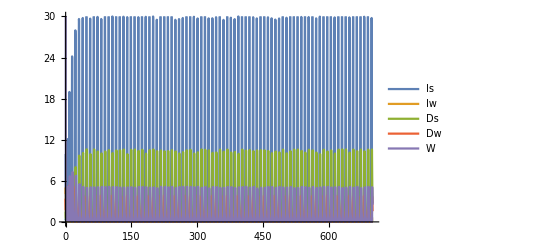

```mathematica
Plot[Evaluate[vart/.ndsol0Func1], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 30}}, PlotLegends->{"Is", "Iw", "Ds","Dw", "W"}]
```

## Mutant dynamics

```mathematica
dImudt = γm M Is  - (d + α)Imu -(Ds+Dw) (ρ+βm)Imu; (*Infected intermediate*)
dDmdt = Imu βm Ds - (μ + σ)Dm;
dMdt = fm Dm - δ M - γm Is M;
```

```mathematica
dMdt > 0
```

Dm fm-Is M γm-M δ>0

```mathematica
Am = {{-d-α - (Ds+Dw) (ρ+βm), 0, γm Is},{βm Ds, -μ -σ, 0},{0, fm, -δ- γm Is}};
Am//MatrixForm
```

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
Am.{Imu, Dm, M} == {dImudt, dDmdt, dMdt}//FullSimplify
```

True

```mathematica
FMat = {{0, 0, 0},{0, 0, 0}, {0, fm, 0}};
```

```mathematica
VMat ={{d+α+(Ds+Dw) (ρ+βm), 0, - Is γm},{-Ds βm, μ + σ, 0}, {0, 0, Is γm + δ}};
```

```mathematica
FMat - VMat == Am//FullSimplify
FMat-VMat//MatrixForm
```

True

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
R0 = Eigenvalues[FMat.Inverse[VMat]][[3]]//FullSimplify
```

(Ds fm Is βm γm)/((Is γm+δ) (d+α+(Ds+Dw) (βm+ρ)) (μ+σ))

R0=fm/(Is γm+δ)(Is  γm)/(d+α+(Ds+Dw) (ρ+βm))(Ds  βm)/(μ+σ)

# Double infections

## ODEs

-Graphics-

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
pFreeCond = {W-> 0, Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0};
pDFreeCond = { Dw-> 0, Dww-> 0};
```

## Predator and transmission functions

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]-> (ρ + βw)(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]-> (ρ + βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]-> (ρ + βw)(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]-> (ρ + βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
```

## Reproduction ratio of a resident (Existence condition for parasite)

```mathematica
MmatRes = {{-(d + αw) - Πw, 0, 0, 0, (1-p)γ Is },{0, -(d + αww)- Πww, 0, 0, p γ Is}, {βw Ds, 2(1-q)βww Ds, -(μ + σw) -(2(1-q)λww +λw), 0, 0}, {0, q βww Ds, (2(1-q)λww + λw), -(μ + σww), 0}, {0, 0, fw, fww, -δ - γ Is}};
(MmatRes/.forceInf).{Iw, Iww, Dw, Dww, W} == {dIwdt, dIwwdt, dDwdt, dDwwdt, dWdt}/.{Πw[Ds, Dw,Dww, βw]-> Πw,Πww[Ds, Dw, Dww,βww]-> Πww }/.forceInf//Simplify
```

True

```mathematica
MmatRes//MatrixForm
```

(-d-αw-Πw | 0 | 0 | 0 | Is (1-p) γ
0 | -d-αww-Πww | 0 | 0 | Is p γ
Ds βw | 2 Ds (1-q) βww | -λw-2 (1-q) λww-μ-σw | 0 | 0
0 | Ds q βww | λw+2 (1-q) λww | -μ-σww | 0
0 | 0 | fw | fww | -Is γ-δ)

```mathematica
MmatRes2 = {{-(d + αw) - Πw, 0, 0, 0, (1-p)γ Is },{0, -(d + αww)- Πww, 0, 0, p γ Is}, {βw Ds, 2(1-q)βww Ds, -(μ + σw)-(2(1-q)λww +λw) , 0, 0}, {βw Dw, q βww Ds +2(1-q)βww Dw, 0, -(μ + σww), 0}, {0, 0, fw, fww, -δ - γ Is}};
MmatRes2.{Iw, Iww, Dw, Dww, W} == {dIwdt, dIwwdt, dDwdt, dDwwdt, dWdt}/.{Πw[Ds, Dw,Dww, βw]-> Πw,Πww[Ds, Dw, Dww,βww]-> Πww }/.forceInf//Simplify
```

True

```mathematica
FmatRes = {{0, 0, 0, 0, 0},{0, 0, 0, 0, 0},{0, 0, 0, 0, 0},{0, 0, 0, 0, 0},{0, 0, fw, fww, 0}} ;
VmatRes = {{(d + αw) + Πw, 0, 0, 0, -(1-p)γ Is },{0, (d + αww)+ Πww, 0, 0, -p γ Is}, {-βw Ds, -2(1-q)βww Ds, (μ + σw) +(2(1-q)λww +λw), 0, 0}, {0,- q βww Ds, -(2(1-q)λww + λw), (μ + σww), 0}, {0, 0, 0, 0, δ + γ Is}};
FmatRes - VmatRes == MmatRes//Simplify
```

True

```mathematica
FmatRes.Inverse[VmatRes]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
(Ds fw βw)/((d+αw+Πw) (λw+2 (1-q) λww+μ+σw))+(fww (Ds βw λw+2 Ds βw λww-2 Ds q βw λww))/((d+αw+Πw) (λw+2 (1-q) λww+μ+σw) (μ+σww)) | (2 Ds fw (1-q) βww)/((d+αww+Πww) (λw+2 (1-q) λww+μ+σw))+(fww (2 Ds βww λw-Ds q βww λw+4 Ds βww λww-6 Ds q βww λww+2 Ds q^2 βww λww+Ds q βww μ+Ds q βww σw))/((d+αww+Πww) (λw+2 (1-q) λww+μ+σw) (μ+σww)) | fw/(λw+2 (1-q) λww+μ+σw)-(fww (-λw-2 (1-q) λww))/((λw+2 (1-q) λww+μ+σw) (μ+σww)) | fww/(μ+σww) | -(fw (-2 Ds Is p (1-q) βww γ (d+αw+Πw)+Ds Is (-1+p) βw γ (d+αww+Πww)))/((Is γ+δ) (d+αw+Πw) (d+αww+Πww) (λw+2 (1-q) λww+μ+σw))+(fww ((-λw-2 (1-q) λww) (-2 Ds Is p (1-q) βww γ (d+αw+Πw)+Ds Is (-1+p) βw γ (d+αww+Πww))+Ds Is p q βww γ (d+αw+Πw) (λw+2 (1-q) λww+μ+σw)))/((Is γ+δ) (d+αw+Πw) (d+αww+Πww) (λw+2 (1-q) λww+μ+σw) (μ+σww)))

```mathematica
VmatRes2 = {{(d + αw) + Πw, 0, 0, 0, -(1-p)γ Is },{0, (d + αww)+ Πww, 0, 0, -p γ Is}, {-βw Ds, -2(1-q)βww Ds, (μ + σw)+(2(1-q)λww +λw) , 0, 0}, {-βw Dw, -q βww Ds -2(1-q)βww Dw, 0, (μ + σww), 0}, {0, 0, 0, 0, δ + γ Is}};
FmatRes - VmatRes2 == MmatRes2//Simplify
```

True

```mathematica
R0Res2 = Eigenvalues[FmatRes.Inverse[VmatRes2]][[5]]//Simplify;
NumR0Res2 = Numerator[R0Res2];
DenomR0Res2 = Denominator[R0Res2];
```

```mathematica
Is γ (Dw fww (λw+2 (1-q) λww+μ+σw)(2 p (1-q) βww(d +αw+ Πw)+(1-p)  βw (d +αww + Πww))  + Ds fww (λw+2 (1-q) λww+μ+σw)p q βww (d+αw+Πw)  +Ds fw  (μ+σww)(2p (1-q) βww (d+αw + Πw)+(1-p )βw(d+αww+ Πww) ))== NumR0Res2//Simplify
```

True

```mathematica
(fww/(Is γ+δ)(p γ)/(d+αww+Πww)Is(2  (1-q) βww)/(μ+σww)Dw+fww/(Is γ+δ) ((1-p)γ)/(d+αw+Πw) Is βw/(μ+σww)Dw+ fww/(Is γ+δ) (p γ)/(d+αww+Πww) Is (q βww)/(μ+σww)Ds +fw/(Is γ+δ) (p γ)/(d+αww+Πww) Is (2 (1-q) βww)/(λw+2 (1-q) λww+μ+σw)Ds + fw/(Is γ+δ) ((1-p )γ)/(d+αw+Πw) Is βw/(λw+2 (1-q) λww+μ+σw)Ds) == R0Res2//Simplify
```

True

```mathematica
fw/(Is γ+δ) ((1-p) γ)/(d+αw+Πw) Is (2 (1-q) βww)/(λw+2 (1-q) λww+μ+σw)Ds
```

(2 Ds fw Is (1-p) (1-q) βww γ)/((Is γ+δ) (d+αw+Πw) (λw+2 (1-q) λww+μ+σw))

```mathematica
FmatRes.Inverse[VmatRes2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
(Ds fw βw)/((d+αw+Πw) (λw+2 (1-q) λww+μ+σw))+(Dw fww βw)/((d+αw+Πw) (μ+σww)) | (2 Ds fw (1-q) βww)/((d+αww+Πww) (λw+2 (1-q) λww+μ+σw))-(fww (-2 Dw (1-q) βww-Ds q βww))/((d+αww+Πww) (μ+σww)) | fw/(λw+2 (1-q) λww+μ+σw) | fww/(μ+σww) | -(fw (-2 Ds Is p (1-q) βww γ (d+αw+Πw)+Ds Is (-1+p) βw γ (d+αww+Πww)))/((Is γ+δ) (d+αw+Πw) (d+αww+Πww) (λw+2 (1-q) λww+μ+σw))-(fww (Is p (-2 Dw (1-q) βww-Ds q βww) γ (d+αw+Πw)+Dw Is (-1+p) βw γ (d+αww+Πww)))/((Is γ+δ) (d+αw+Πw) (d+αww+Πww) (μ+σww)))

```mathematica
R0Res = Eigenvalues[FmatRes.Inverse[VmatRes]][[5]]//Simplify;
```

```mathematica
NumR0Res = Numerator[R0Res];
DenomR0Res = Denominator[R0Res]
```

(Is γ+δ) (d+αw+Πw) (d+αww+Πww) (λw-2 (-1+q) λww+μ+σw) (μ+σww)

```mathematica
Ds Is γ (fww ( (1-p) βw (λw+2 (1-q) λww)(d + αww + Πww)+ (p  βww 2(1-q)( λw+2  (1-q) λww) + p  βww q( λw+2  (1-q) λww+μ+σw))(αw + Πw + d))+fw (μ+σww)((1-p) (αww  + d + Πww)βw+ 2 p (1-q) (αw + d + Πw) βww  ) )==NumR0Res//Simplify
```

True

```mathematica
((βw Iw+2 (1-q) βww Iww)  βw)/((λw+2 (1-q) λww+μ+σw) (μ+σww))Ds fww/(Is γ+δ) ((1-p)γ)/(d+αw+Πw)Is+  (( λw+2  (1-q) λww) 2(1-q)βww)/((λw+2 (1-q) λww+μ+σw) (μ+σww))Ds fww/(Is γ+δ)(p γ)/(d+αww+Πww)Is+(q βww)/(μ + σww)Ds fww/(Is γ+δ)(p γ)/(d + αww + Πww)Is+(q βww)/(μ + σww)Ds fww/(Is γ+δ)((1-p) γ)/(d + αw + Πw)Is+βw/(λw+2 (1-q) λww+μ+σw)Ds fw/(Is γ+δ)(γ(1-p))/(d+αw+Πw)Is+(2  (1-q)  βww)/(λw-2 (-1+q) λww+μ+σw) Ds fw/(Is γ+δ)(γ p)/(d+αww+Πww)Is== R0Res//Simplify
```

(Ds fww Is (-1+p) γ (Iw βw^2-2 Iww (-1+q) βw βww-βw λw+q βww λw-2 βw λww+2 q βw λww+2 q βww λww-2 q^2 βww λww+q βww μ+q βww σw))/((Is γ+δ) (d+αw+Πw) (λw-2 (-1+q) λww+μ+σw) (μ+σww))==0

```mathematica
R0freePar = R0Res/.λw-> 0/.λww-> 0//FullSimplify;
```

## Simple analytical results (linear birth functions)

Solution where both the intermediate and definitive hosts are free of parasites:

```mathematica
solRes0 = Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func0/.forceInf/.pFreeCond, varRes]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→0,Ds→0},{Is→μ/(c ρ),Ds→-(d-r)/ρ}}

Solution where infected definitive hosts do not exist (Note this solution is not biologically meaningful because I_s is always negative):

```mathematica
solResD0 =  Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func0/.forceInf/.pDFreeCond, varRes]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→0,Iw→0,Iww→0,Ds→0,W→0},{Is→-δ/γ,Iw→-((-1+p) (d-r) (d+αww) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Iww→(p (d-r) (d+αw) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Ds→0,W→-((d-r) (d+αw) (d+αww))/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ)},{Is→μ/(c ρ),Iw→0,Iww→0,Ds→(-d+r)/ρ,W→0}}

## Condition for positive parasite population (linear birth functions)

```mathematica
(*R0freePar/.Πw-> Πw[Ds,Dw,Dww,βw]/.Πww -> Πww[Ds,Dw,Dww,βww]/.func0/.solRes0[[2]]/.pDFreeCond;
Reduce[% > 1 && fw > 0 && fww > 0 && r > 0 && d >0 && γ > 0&&1>p>0&&1>q>0&&βw > 0 && βww > 0 &&ρ > 0 && μ >0 && σw >= 0 && σww >= 0 &&αw >= 0 && αww >=0 && c > 0 && δ > 0 && r > d, Reals];*)(*I comment this code because the calculartion time is too long *)
```

```mathematica
condParasiteInv1 = {γ>-((c δ ρ (-d βw+αw ρ+r (βw+ρ)) (-d βww+αww ρ+r (βww+ρ)) (μ+σw) (μ+σww))/(μ (fw r ((-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(αw ρ+r (βw+ρ)) (μ+σw) (-fww p q r βww+(αww ρ+r (βww+ρ)) (μ+σww))+d^2 βw βww (fw (-1+p q) (μ+σww)+(μ+σw) (-fww p q+μ+σww))-d (fw (2 (-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(μ+σw) (-fww p q βww (αw ρ+r (2 βw+ρ))+(2 r βw βww+r βw ρ+αww βw ρ+r βww ρ+αw βww ρ) (μ+σww)))))), fw>((d βw-αw ρ-r (βw+ρ)) (μ+σw) (-fww p q r βww+d βww (fww p q-μ-σww)+(αww ρ+r (βww+ρ)) (μ+σww)))/((d-r) (d (-1+p q) βw βww+αww (βw-p βw) ρ-p (-1+q) r βww ρ-p (-1+q) αw βww ρ+r βw (βww-p q βww+ρ-p ρ)) (μ+σww)), fww<((d βww-αww ρ-r (βww+ρ)) (μ+σww))/(p q (d-r) βww)};
condParasiteInv2 = {γ>-((c δ ρ (-d βw+αw ρ+r (βw+ρ)) (-d βww+αww ρ+r (βww+ρ)) (μ+σw) (μ+σww))/(μ (fw r ((-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(αw ρ+r (βw+ρ)) (μ+σw) (-fww p q r βww+(αww ρ+r (βww+ρ)) (μ+σww))+d^2 βw βww (fw (-1+p q) (μ+σww)+(μ+σw) (-fww p q+μ+σww))-d (fw (2 (-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(μ+σw) (-fww p q βww (αw ρ+r (2 βw+ρ))+(2 r βw βww+r βw ρ+αww βw ρ+r βww ρ+αw βww ρ) (μ+σww)))))), fww>=((d βww-αww ρ-r (βww+ρ)) (μ+σww))/(p q (d-r) βww)};
```

## Stability of disease free equilibrium (linear birth function)

```mathematica
Jmat = D[odesRes/.func0/.forceInf, {varRes}];
```

```mathematica
Jmat/.solRes0[[2]]/.pFreeCond//MatrixForm
eivPF = Eigenvalues[%]//FullSimplify
```

(0 | r | r | -μ/c | -μ/c | -μ/c | -(γ μ)/(c ρ)
0 | -d-αw+((d-r) (βw+ρ))/ρ | 0 | 0 | 0 | 0 | ((1-p) γ μ)/(c ρ)
0 | 0 | -d-αww+((d-r) (βww+ρ))/ρ | 0 | 0 | 0 | (p γ μ)/(c ρ)
-c (d-r) | -c (d-r)+((d-r) βw)/ρ | -c (d-r)+((d-r) βww)/ρ | 0 | μ | μ | 0
0 | -((d-r) βw)/ρ | -(2 (1-q) (d-r) βww)/ρ | 0 | -μ-σw | 0 | 0
0 | 0 | -(q (d-r) βww)/ρ | 0 | 0 | -μ-σww | 0
0 | 0 | 0 | 0 | fw | fww | -δ-(γ μ)/(c ρ))

{-√(d-r) √μ,√(d-r) √μ,Root[261+#1^5&,1]/(c ρ^5),Root[1&,2]/(c ρ^5),Root[1&,3]/(c ρ^5),Root[261+#1^5&,4]/(c ρ^5),Root[-c^4 d^2 fw βw βww γ μ^2 ρ^22-c^4 d^2 fw p βw βww γ μ^2 ρ^22+258+#1^5&,5]/(c ρ^5)}
 |  |  |  |

```mathematica
Jmat/.Thread[varRes-> 0]//MatrixForm
eivExtinct = Eigenvalues[%]//FullSimplify
```

(-d+r | r | r | 0 | 0 | 0 | 0
0 | -d-αw | 0 | 0 | 0 | 0 | 0
0 | 0 | -d-αww | 0 | 0 | 0 | 0
0 | 0 | 0 | -μ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ-σw | 0 | 0
0 | 0 | 0 | 0 | 0 | -μ-σww | 0
0 | 0 | 0 | 0 | fw | fww | -δ)

{-d+r,-d-αw,-d-αww,-δ,-μ,-μ-σw,-μ-σww}

## Numerical results func0 (linear functions)

## General view

```mathematica
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

```mathematica
sys = makeSystem[varRes, vartRes, odesRes/.func0/.forceInf];
sysfunc0 = odesRes/.forceInf/.func0;
```

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};
```

{{-5.67289×10^-29,-6.30321×10^-30,5.43339×10^-30,4.94844×10^-33,-2.95824×10^-27}}

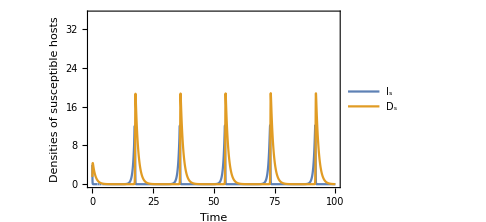
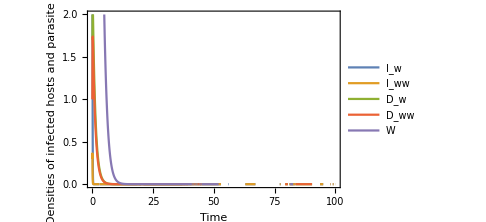
-Graphics- | -Graphics-

```mathematica
maxt = 100;
init0= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};
sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sys/.prEco0, init0], varRes, {t, 0, maxt}] ;
p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 35}}, PlotLegends->{"I_s",  "D_s"}, Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->Medium];
Evaluate[{Iw[maxt], Iww[maxt], Dw[maxt], Dww[maxt],W[maxt]}/.ndsol0]
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 2}},PlotLegends->{"I_w", "I_ww", "D_w", "D_ww", "W"},Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->Medium];
Grid[{{p1, p2}}]
(*Export["diseasefree_linear.jpg",%]*)
```

## Bifurcation parameter γ

```mathematica
parγ = {ρ -> 1.2, d -> 0.1,r -> 2.5, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1};
γrange = Range[0.1, 8, 0.05];
```

```mathematica
solsγ = NSolve[Thread[(odesRes/.func0/.forceInf/.parγ/.γ-> 0.1) == 0], varRes];
eqinit = {Is->1.1309523809523814,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};
```

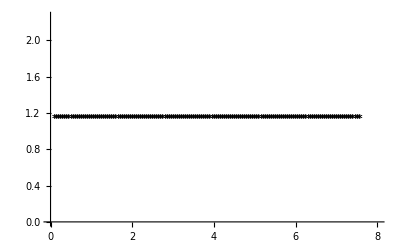

```mathematica
eqγzero = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, eqinit];
{#}& /@Transpose[{γrange, Is/.eqγzero}];
p0 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγzero], PlotStyle-> Black];
{#}& /@Transpose[{γrange, Ds/.eqγzero}];
p1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγzero], PlotStyle-> Gray];
Show[p0, p1]
```

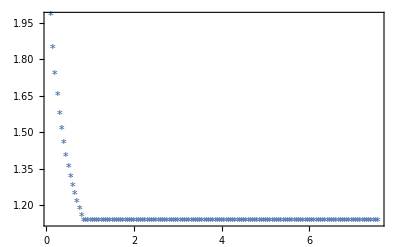

```mathematica
colordata = ColorData[97, "ColorList"];
varname = Is;
eqγ1 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[1]]];
{#}& /@Transpose[{γrange, varname/.eqγ1}];
pγ1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ1], PlotStyle-> colordata[[1]]];
eqγ2 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[2]]];
{#}& /@Transpose[{γrange, varname/.eqγ2}];
pγ2 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ2], PlotStyle-> colordata[[2]]];
eqγ13 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[13]]];
{#}& /@Transpose[{γrange, varname/.eqγ13}];
pγ13 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ13], PlotStyle-> colordata[[3]]];
eqγ16 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[16]]];
{#}& /@Transpose[{γrange, varname/.eqγ16}];
pγ16 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ16], PlotStyle-> colordata[[4]]];
eqγ17 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[17]]];
{#}& /@Transpose[{γrange, varname/.eqγ17}];
pγ17 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ17], PlotStyle-> colordata[[5]]];
Show[pγ1, pγ2, pγ13,pγ16,pγ17,PlotRange-> All, Frame-> True, FrameLabel-> {"Infection rate of free parasite (γ)", "Density of population"}]
```

## Bifurcation parameter βw (linear birth functions)

```mathematica
parβw = {ρ -> 1.2, d -> 0.1,r -> 2.5, γ -> 3.5, αw-> 0, αww-> 0,  βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1, Κ-> 100};
βwrange = Range[1.5, 14.5, 0.1];
```

```mathematica
solsβw = NSolve[Thread[(odesRes/.func0/.forceInf/.parβw/.βw-> 1.5) == 0], varRes];
```

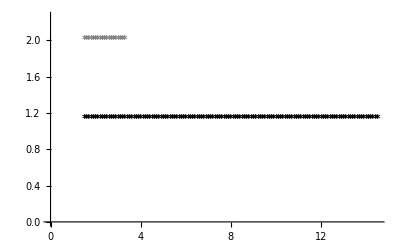

```mathematica
eqinit = {Is->1.1309523809523812,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};
eqβwzero = FollowRoot[sysfunc0, parβw, βw, βwrange, varRes, eqinit];
{#}& /@Transpose[{βwrange, Is/.eqβwzero}];
p0 = ListPlot[%, PlotMarkers->ListMark[Jmat, parβw, βw, βwrange, eqβwzero], PlotStyle-> Black];
{#}& /@Transpose[{βwrange, Ds/.eqβwzero}];
p1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parβw, βw, βwrange, eqβwzero], PlotStyle-> Gray];
Show[p0, p1]
```

## Stability of disease free equilibrium (nonlinear birth functions)

```mathematica
solRes1 = Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func1/.forceInf/.pFreeCond, varRes]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→(-d+r)/(k r),Ds→0},{Is→0,Ds→0},{Is→μ/(c ρ),Ds→(-k r μ+c (-d+r) ρ)/(c ρ^2)}}

```mathematica
Reduce[(Ds/.solRes1[[3]]) > 0 && ρ > 0 && c > 0 && d  > 0 && μ > 0 && r > 0 && k >0, k, Reals]
```

r>0&&0<d<r&&ρ>0&&μ>0&&c>0&&0<k<(-c d ρ+c r ρ)/(r μ)

```mathematica
Jmat = D[odesRes/.func1/.forceInf, {varRes}];
```

```mathematica
Jmat/.pFreeCond;
eivPF = Eigenvalues[%]/.solRes1[[3]]
```

{1/2 (-d+r-(2 k r μ)/(c ρ)-(-k r μ+c (-d+r) ρ)/(c ρ)-√(-(4 μ (-k r μ+c (-d+r) ρ))/(c ρ)+(d-r+(2 k r μ)/(c ρ)+(-k r μ+c (1) ρ)/(c ρ))^2)),1/2 (-d+r-1-1/(c ρ)+√(-1/(c ρ)+(1)^2)),3,Root[1],Root[r^2 δ μ^2+r αw δ μ^2+542+#1^5&,5]}
 |  |  |  |

```mathematica
Simplify[Reduce[eivPF[[1]]<0 &&eivPF[[2]]<0   && ρ > 0&&d > 0 && c > 0 && k > 0 && r > 0 && r > d && μ > 0 ,   k], c > 0 && r > 0 && ρ > 0 && μ > 0]
condPfreeStableNL = %[[2]]
```

0<d<r&&(2 c (-1+√((-d+r+μ)/μ)) ρ)/r≤k<(c (-d+r) ρ)/(r μ)

(2 c (-1+√((-d+r+μ)/μ)) ρ)/r≤k<(c (-d+r) ρ)/(r μ)

```mathematica
Reduce[condPfreeStableNL[[1]] < condPfreeStableNL[[3]] && c > 0 && r > 0 && ρ > 0 && μ > 0 && r > d]
```

ρ>0&&r>0&&k>0&&c>0&&d<r&&μ>(-4 c^2 d ρ^2+4 c^2 r ρ^2)/(k^2 r^2+4 c k r ρ)

## Condition for positive parasite population (nonlinear birth functions)

```mathematica
R0freePar/.{αw -> α, αww -> α}/.{σw -> σ, σww -> σ}/.{fww-> f, fw-> f};
```

```mathematica
R0freePar/.{αw -> α, αww -> α}/.{σw -> σ, σww -> σ}/.{fww-> f, fw-> f}/.Πw-> Πw[Ds,Dw,Dww,βw]/.Πww -> Πww[Ds,Dw,Dww,βww]/.func1/.solRes1[[3]]/.pFreeCond//FullSimplify;
condPspreadNL = Reduce[% > 1 && 1>p> 0 && 1>q>0 && k<(c (-d+r) ρ)/(r μ)&&f > 0 && r > d && γ > 0 && c > 0 && d > 0 && βw >0&&βww>0&& r > 0 && d > 0 && δ > 0 && α >= 0 && μ>0 && ρ > 0 &&σ >= 0, f];
condPspreadNL [[15]]//FullSimplify
```

f>-(((γ μ+c δ ρ) (k r μ (βw+ρ)-c ρ (-d βw+r βw+(r+α) ρ)) (k r μ (βww+ρ)-c ρ (-d βww+r βww+(r+α) ρ)) (μ+σ))/(γ μ (k r μ+c (d-r) ρ) (k r μ ((-1+p (-1+q)) βw βww+(-1+p) βw ρ+p (-2+q) βww ρ)+c ρ ((-1+p (-1+q)) (d-r) βw βww-(r+α) ((-1+p) βw+p (-2+q) βww) ρ))))

```mathematica
R0freePar/.{αw -> α, αww -> α}/.{σw -> σ, σww -> σ}/.fww->ϵ fw/.Πw-> Πw[Ds,Dw,Dww,βw]/.Πww -> Πww[Ds,Dw,Dww,βww]/.func1/.solRes1[[3]]/.pFreeCond//FullSimplify;
condPspreadNL2 = Reduce[% > 1 && 1>p> 0 && 1>q>0 && k<(c (-d+r) ρ)/(r μ)&&fw > 0 && r > d && γ > 0 && c > 0 && d > 0 && βw >0&&βww>0&& r > 0 && d > 0 && δ > 0 && α >= 0 && μ>0 && ρ > 0 &&σ >= 0 && ϵ > 0, fw];
condPspreadNL2[[16]]//FullSimplify
```

fw>((γ μ+c δ ρ) (k r μ (βw+ρ)-c ρ (-d βw+r βw+(r+α) ρ)) (k r μ (βww+ρ)-c ρ (-d βww+r βww+(r+α) ρ)) (μ+σ))/(γ μ (k r μ+c (d-r) ρ) (c ρ ((d-r) βw βww (1+p+p q (-2+ϵ))+(r+α) ((-1+p) βw-p βww (2+q (-2+ϵ))) ρ)+k r μ (p βww (2+q (-2+ϵ)) ρ+βw (βww (1+p+p q (-2+ϵ))+ρ-p ρ))))

## Numerical analysis (non-linear birth function)

```mathematica
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
sys = makeSystem[varRes, vartRes, odesRes/.func1/.forceInf];
sysfunc1 = odesRes/.func1/.forceInf;
```

## Disease-free equilibrium

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26};
```

```mathematica
condPfreeStableNL/.prEcoNL
```

True

{{2.32143,0.0758929}}

{{3.83477×10^-12,4.26085×10^-13,-1.87027×10^-13,-1.70779×10^-16,-3.45379×10^-12}}

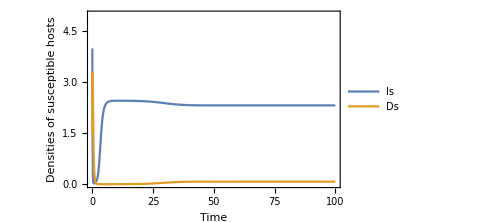
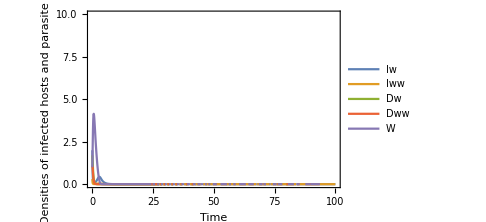
-Graphics- | -Graphics-

```mathematica
maxt = 100;
initNL= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 1};
solsNL = NSolve[Thread[(odesRes/.func1/.forceInf/.prEcoNL) == 0], varRes];
ndsolNL = NDSolve[Join[sys/.prEcoNL, initNL], varRes, {t, 0, maxt}] ;
p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->Medium];
Evaluate[{Is[maxt], Ds[maxt]}/.ndsolNL]
Evaluate[{Iw[maxt], Iww[maxt], Dw[maxt], Dww[maxt],W[maxt]}/.ndsolNL]
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolNL], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 10}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->Medium];
Grid[{{p1, p2}}]
(*Export["Diseasefree.jpeg",%]*)
```

```mathematica
solsNL[[18]]
```

{Is→2.32143,Iw→0,Iww→0,Ds→0.0758929,Dw→0,Dww→0,W→0}

```mathematica
Eigenvalues[Jmat/.prEcoNL/.solsNL[[18]]]
```

{-7.33727,-4.49395,-3.9,-1.21711,-1.10491,-0.805839,-0.291822}

## Disease-stable equilibrium

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, fw -> 40.4122, fww-> 40.4122*1.95,δ-> 0.9, k -> 0.26};
```

```mathematica
condPspreadNL/.prEcoDSNL/.α-> 0/.σ -> 0
```

f>39.0477

```mathematica
condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};
```

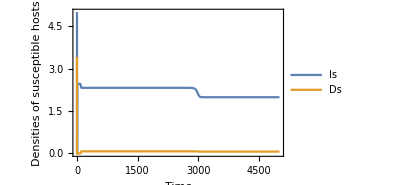
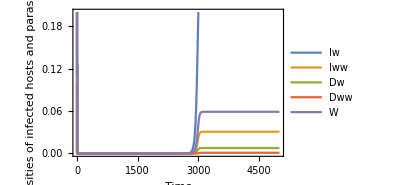
-Graphics- | -Graphics-

{{1.98959,0.276986,0.0307762,0.0674071,0.00775324,0.00101567,0.0589767}}

```mathematica
maxt = 5000;
imsize = 300;
{Is[0]== 17.6, Iw[0] == 1.2,Iww[0]==0.32, Ds[0] ==3.4, Dw[0] == 1.7,Dww[0]==0.1, W[0] == 0.1};
ndsolDS = NDSolve[Join[sys/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt}, AccuracyGoal->Infinity] ;
solsDS = NSolve[Thread[(odesRes/.condsimplifyNL/.func1/.forceInf/.prEcoDSNL) == 0], varRes, Reals];
p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolDS], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imsize];
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolDS], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 0.2}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imsize];
Grid[{{p1, p2}}]
Evaluate[{ Is[maxt], Iw[maxt], Iww[maxt],Ds[maxt], Dw[maxt], Dww[maxt],W[maxt]}/.ndsolDS]
```

```mathematica
Select[solsDS, (Is/.#)>0 && (Iw/.#)>0 && (Iww/.#)>0 && (W /.#)>0&]
Eigenvalues[Jmat/.condsimplifyNL/.%/.prEcoDSNL]
```

{{Is→1.98959,Iw→0.276986,Iww→0.0307762,Ds→0.0674071,Dw→0.00775324,Dww→0.00101567,W→0.0589767}}

{-5.89989+1.86018 ⅈ,-5.89989-1.86018 ⅈ,-4.90402+0. ⅈ,-1.15961+0. ⅈ,-1.10568+0. ⅈ,-0.316399+0. ⅈ,-0.053656+0. ⅈ}

```mathematica
solsDS[[1]]
```

{Is→-68421.6,Iw→137782.,Iww→-69588.4,Ds→0.00124543,Dw→-0.686767,Dww→0.352188,W→0}

```mathematica
xx == {}
```

xx=={}

```mathematica
And[x,y,z]
```

x&&y&&z

```mathematica
Select[solsDS,And@@Thread[(varRes/.# )> 0]&][[1]]
```

{Is→1.98959,Iw→0.276986,Iww→0.0307762,Ds→0.0674071,Dw→0.00775324,Dww→0.00101567,W→0.0589767}

```mathematica
And@@Thread[varRes> 0]
```

Is>0&&Iw>0&&Iww>0&&Ds>0&&Dw>0&&Dww>0&&W>0

```mathematica
Select[solsDS, (Is/.#)>0 && (Ds/.#)>0 && (Iw/.#)==0 && (Iww/.#)==0 && (Dw /.#)==0 && (Dww/.#)==0 && (W/.#)==0 &]
Eigenvalues[Jmat/.condsimplifyNL/.%/.prEcoDSNL]
```

{{Is→2.32143,Iw→0,Iww→0,Ds→0.0758929,Dw→0,Dww→0,W→0}}

{-6.33228+1.6607 ⅈ,-6.33228-1.6607 ⅈ,-3.9+0. ⅈ,-1.21711+0. ⅈ,-1.10491+0. ⅈ,-0.291822+0. ⅈ,0.0275041+0. ⅈ}

```mathematica
Eigenvalues[Jmat/.condsimplifyNL/.solsDS[[20]]/.prEcoDSNL]
```

{-6.64693+1.26685 ⅈ,-6.64693-1.26685 ⅈ,-3.10432+0. ⅈ,-1.28285+0. ⅈ,-1.09493+0. ⅈ,-0.144473+0. ⅈ,-0.102248+0. ⅈ}

## Bifurcation fw

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 2};
fwrangeFWrd = Range[40.5, 51.5, 0.05];
fwrangeBWrd = Range[40.5, 32, -0.05];
fwrange = Range[32, 51.5, 0.3];
```

```mathematica
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 40.5) == 0], varRes, Reals];
```

```mathematica
solsfw= Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];
```

```mathematica
solsfw
```

{Is→1.94998,Iw→0.310361,Iww→0.0344846,Ds→0.0663516,Dw→0.00843452,Dww→0.00123713,W→0.0674004}

```mathematica
{Is->1.9499789231930884,Iw->1.9499789231930884`1,Iww->0.034484565050009165,Ds->0.06635159476098869,Dw->0.008434519849083872,Dww->0.0012371277216552442,W->0.06740038429262239}
```

{Is→1.94998,Iw→2.,Iww→0.0344846,Ds→0.0663516,Dw→0.00843452,Dww→0.00123713,W→0.0674004}

```mathematica
eqfwFWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeFWrd, varRes, solsfw];
```

```mathematica
eqfwBWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeBWrd, varRes, solsfw];
```

FindRoot::reged: The point {2.31975,0.00138535,0.000153927,0.0758543,0.0000494171,0.,0.000252349} is at the edge of the search region {0.,∞} in coordinate 6 and the computed search direction points outside the region.

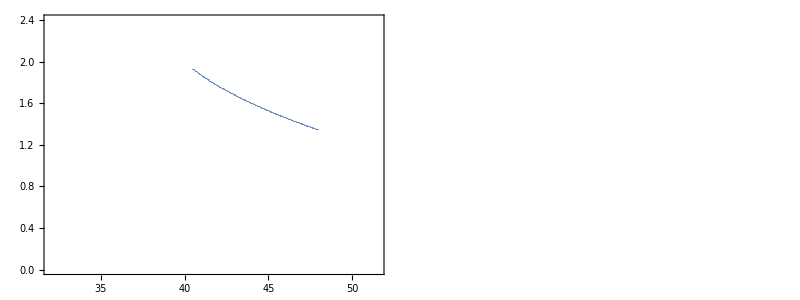

```mathematica
rangeIs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {0, 2.4}};
rangeDs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {0, 0.1}};
imsize = 300;
xaxis =fwrangeFWrd[[1;; Length[eqfwFWrd]]];
 {#}& /@Transpose[{xaxis, Is/.eqfwFWrd}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmat/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imsize, Frame-> {{True, False}, {True,False}}, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium I_s"}];
{#}& /@Transpose[{xaxis, Ds/.eqfwFWrd}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmat/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle-> colorlist[[2]], PlotRange->rangeDs, ImageSize->imsize, Frame-> {{True, False}, {True,False}}, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium D_s"}];
xaxis = fwrangeBWrd[[1;;Length[eqfwBWrd]]];
{#}& /@Transpose[{xaxis, Is/.eqfwBWrd}];
p2 = ListPlot[%, PlotMarkers->ListStableMark[Jmat/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imsize];
{#}& /@Transpose[{xaxis, Ds/.eqfwBWrd}];
p3 = ListPlot[%, PlotMarkers->ListStableMark[Jmat/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imsize];
eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
{#}& /@Transpose[{fwrange, Is/.eqfwzero}];
p4 = ListPlot[%, PlotMarkers->ListStableMark[Jmat/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imsize];
{#}& /@Transpose[{fwrange, Ds/.eqfwzero}];
p5 = ListPlot[%, PlotMarkers->ListStableMark[Jmat/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imsize];
pp0 = Show[p0,  p2, p4];
pp1 = Show[p1, p3, p5];
Grid[{{pp0, pp1}}]
```

Find value of the bifurcation point

```mathematica
rr= Range[39, 40, 0.0002];
FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, rr, varRes, solsfwzero];
xx =ListStableMark[Jmat/.fww-> ϵ fw, parfw, fw, rr, %];
pos = Position[xx, "*", 1, 1][[1]][[1]];
xx[[pos]] == "*"
xx[[pos-1]] == "." 
fwbifur = rr[[pos]]
```

True

True

39.0122

## Bifurcation ϵ and fw (fww = ϵ fw)

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26};
solsinitAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parϵfw/.ϵ-> 2/.fw-> fwbifur) == 0], varRes, Reals];
solspositive =  Select[solsinitAll, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];
solszero = Select[solsinitAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];
```

```mathematica
ϵrangeBWrd = Range[2, 0.01, -0.1];
fwrangeBWrd = Range[fwbifur, 32, -0.5];
fwrangeFWrd = Range[fwbifur, 50, 0.5];
```

```mathematica
eqlϵfwBW = FollowNSolveTwoParameters[sysfunc1/.fww-> ϵ fw, parϵfw, ϵ, ϵrangeBWrd, fw, fwrangeBWrd, varRes]
```

$Aborted

```mathematica
yy = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ-> i}, {fw-> j}, ϵfw, varRes], {i, 2, 1, -0.5}, {j, fwbifur, 40, 0.2}]//AbsoluteTiming
```

{11.1261,{{{ϵfw→{2.,39.0122},Is→2.27708,Iw→0.0367187,Iww→0.00407985,Ds→0.0748472,Dw→0.00126774,Dww→0.0000230171,W→0.00683053},{ϵfw→{2.,39.2122},Is→2.17697,Iw→0.119973,Iww→0.0133304,Ds→0.0723464,Dw→0.00385569,Dww→0.000220766,W→0.0233604},{ϵfw→{2.,39.4122},Is→2.12511,Iw→0.163283,Iww→0.0181425,Ds→0.0709998,Dw→0.00505269,Dww→0.000392078,W→0.032571},{ϵfw→{2.,39.6122},Is→2.0841,Iw→0.197609,Iww→0.0219566,Ds→0.0699202,Dw→0.00593315,Dww→0.000556052,W→0.0401904},{ϵfw→{2.,39.8122},Is→2.04881,Iw→0.227211,Iww→0.0252457,Ds→0.0689842,Dw→0.00664614,Dww→0.000715273,W→0.0469997}},{{ϵfw→{1.5,39.2122},Is→2.29599,Iw→0.0210496,Iww→0.00233884,Ds→0.0752988,Dw→0.00073646,Dww→7.95144×10^-6,W→0.00388256},{ϵfw→{1.5,39.4122},Is→2.27012,Iw→0.0424926,Iww→0.0047214,Ds→0.074679,Dw→0.0014599,Dww→0.0000304649,W→0.00792947},{ϵfw→{1.5,39.6122},Is→2.24591,Iw→0.0625906,Iww→0.00695451,Ds→0.0740864,Dw→0.0021138,Dww→0.0000640626,W→0.0118086},{ϵfw→{1.5,39.8122},Is→2.22303,Iw→0.0816088,Iww→0.00906765,Ds→0.0735168,Dw→0.00271138,Dww→0.000106392,W→0.0155577}},{{ϵfw→{1.,39.2122},Is→2.31013,Iw→0.00934686,Iww→0.00103854,Ds→0.075631,Dw→0.000330256,Dww→1.75055×10^-6,W→0.00171313},{ϵfw→{1.,39.4122},Is→2.29662,Iw→0.0205275,Iww→0.00228083,Ds→0.0753137,Dw→0.00071851,Dww→7.58147×10^-6,W→0.0037852},{ϵfw→{1.,39.6122},Is→2.28335,Iw→0.0315218,Iww→0.00350242,Ds→0.0749978,Dw→0.00109312,Dww→0.0000171786,W→0.00584726},{ϵfw→{1.,39.8122},Is→2.27031,Iw→0.0423415,Iww→0.00470461,Ds→0.0746834,Dw→0.0014549,Dww→0.0000302572,W→0.00790061}}}}

```mathematica
eqlϵBWfwFW2 = FollowRootTwoParameters[sysfunc1/.fww-> ϵ fw, parϵfw, ϵ, ϵrangeBWrd, fw,fwrangeFWrd, varRes, solspositive, {0, 0, 0, 0, 0, 10^-10, 0 }, 1000, Infinity]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{Is→2.27708,Iw→0.0367187,Iww→0.00407985,Ds→0.0748472,Dw→0.00126774,Dww→0.0000230171,W→0.00683053}}

```mathematica
eqlϵBWfwFW = FollowNSolveTwoParameters[sysfunc1/.fww-> ϵ fw,parϵfw,ϵ,ϵrangeBWrd,fw, fwrangeFWrd,varRes]//AbsoluteTiming
```

$Aborted

```mathematica
xaxis = ϵrangeBWrd[[1;;Length[eqlϵBWfwFW[[2]]]]];
yaxis = fwrangeFWrd[[1;;Length[eqlϵBWfwFW[[2]]]]];
ListStableMarkTwoParameters[Jmat/fww-> ϵ fw, parϵfw, ϵ,ϵrangeBWrd,fw, yaxis, eqlϵBWfwFW[[2]], False ]
```

Part::take: Cannot take positions 1 through 110 in {2.,1.95,1.9,1.85,1.8,1.75,1.7,1.65,1.6,1.55,«30»}.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 2} and {2, 3} of MapThread[SingleStableMark,{{{{Power[«2»] Plus[«5»],Power[«2»] Plus[«2»],Power[«2»] Plus[«2»],-Power[«2»] Is ρ,-Power[«2»] Is ρ,-Power[«2»] Is ρ,-Power[«2»] Is γ},«5»,{-Power[«2»] W γ,0,0,0,fw Power[«2»],1,Power[«2»] Plus[«2»]}}→fw ϵ,«9»,«100»},«2»,{{«1»},«9»,«100»}}]; dimensions are 110 and 4400.

{{{2.,39.0122},{2.,39.1122},{2.,39.2122},{2.,39.3122},{2.,39.4122},{2.,39.5122},{2.,39.6122},{2.,39.7122},{2.,39.8122},{2.,39.9122},{2.,40.0122},{2.,40.1122},{2.,40.2122},{2.,40.3122},{2.,40.4122},{2.,40.5122},{2.,40.6122},{2.,40.7122},{2.,40.8122},{2.,40.9122},{2.,41.0122},4358,{0.05,47.9122},{0.05,48.0122},{0.05,48.1122},{0.05,48.2122},{0.05,48.3122},{0.05,48.4122},{0.05,48.5122},{0.05,48.6122},{0.05,48.7122},{0.05,48.8122},{0.05,48.9122},{0.05,49.0122},{0.05,49.1122},{0.05,49.2122},{0.05,49.3122},{0.05,49.4122},{0.05,49.5122},{0.05,49.6122},{0.05,49.7122},{0.05,49.8122},{0.05,49.9122}},1}
 |  |  |  |

MapThread::mptc: Incompatible dimensions of objects at positions {2, 2} and {2, 3} of MapThread[SingleStableMark,{{{{Power[«2»] Plus[«5»],Power[«2»] Plus[«2»],Power[«2»] Plus[«2»],-Power[«2»] Is ρ,-Power[«2»] Is ρ,-Power[«2»] Is ρ,-Power[«2»] Is γ},«5»,{-Power[«2»] W γ,0,0,0,fw Power[«2»],1,Power[«2»] Plus[«2»]}}→fw ϵ,«9»,«100»},«2»,{{«1»},«9»,«100»}}]; dimensions are 110 and 4400.

```mathematica
rangeϵfw= {{ϵrangeBWrd[[-1]], ϵrangeBWrd[[1]]}, {fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}};
imsize = 300;
xaxis = ϵrangeBWrd[[1;;Length[eqlϵfwBW]]];
yaxis = fwrangeBWrd[[1;;Length[eqlϵfwBW]]];
smlp = ListStableMarkTwoParameters[Jmat/.fww-> ϵ fw, parϵfw, ϵ, xaxis,fw, yaxis, eqlϵfwBW, False];
eqlϵfwzeroBW = ConstantArray[solszero, Length[ϵrangeBWrd]*Length[fwrangeBWrd]];
sml0 = ListStableMarkTwoParameters[Jmat/.fww-> ϵ fw, parϵfw, ϵ, ϵrangeBWrd,fw, fwrangeBWrd, eqlϵfwzeroBW, False ];
p0 = ListPlot[smlp[[1]],  PlotMarkers->smlp[[2]], PlotRange->rangeϵfw, ImageSize->imsize, Frame-> {{True, False}, {True,False}}, FrameLabel->{"ϵ", "fw"}];
p1 = ListPlot[sml0[[1]], PlotMarkers->sml0[[2]], PlotStyle->Black, PlotRange->rangeϵfw, ImageSize->imsize, Frame-> {{True, False}, {True,False}}, FrameLabel->{"ϵ", "fw"}];
yaxis = fwrangeFWrd[[1;;Length[eqlϵBWfwFW]]];
smlp = ListStableMarkTwoParameters
Show[p0, p1]
```

-Graphics-

## Mutant dynamics

```mathematica
2p (M W)/(M + W)^2+ p M^2/(M+W)^2+(1-p)W/(M + W)+(1-p)M/(M+W)+p W^2/(M + W)^2//FullSimplify
```

1

```mathematica
dImdt = (1-p)ηm Is - (d + αm) Imut - Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw]Imut;
dImmdt = p ηmm Is - (d + αmm) Imm - Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw]Imm;
dImwdt = p ηmw Is - (d + αmw) Imw - Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw]Imw;
dDmdt =( λm + (1-q)(λmm + λmw))Ds - (μ + σm) Dm - (λw + λm+ (1-q)(λww + λmw+λmm) )Dm;
dDmmdt = q λmm Ds + (λm + (1-q)(λmm + λmw))Dm -(μ + σmm)Dmm;
dDmwdt = q λmw Ds + (λm + (1-q)(λmm + λmw))Dw + (λw + (1-q)(λww + λmw))Dm - (μ + σmw) Dmw;
dMdt = fm Dm + fmm Dmm + fmw Dmw - δ M - (ηm + ηmw + ηmm)Is;
odesMut = {dImdt, dImmdt, dImwdt, dDmdt, dDmmdt, dDmwdt, dMdt};
varMut = {Imut,  Imm,Imw, Dm, Dmm, Dmw, M};
forceInfMut = {ηm -> γ M/(M+W)(M + W), ηmm ->γ M^2/(M+W)^2(M + W), ηmw ->  γ 2 (M W)/(M + W)^2(M + W), λm -> βm Imut, λmw -> βmw Imw, λmm -> βmm Imm, λw -> βw Iw, λww -> βww Iww};
```

```mathematica
Mmat ={ {- (d + αm)- Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw], 0, 0, 0, 0, 0, (1-p)γ Is},
{0, - (d + αmm)- Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw], 0, 0, 0, 0, p γ M/(M+W)Is}, {0, 0, - (d + αmw) - Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw], 0, 0, 0, p γ 2 W/(M + W)Is}, {βm Ds, (1-q)βmm Ds, (1-q)βmw Ds, - (μ + σm)- (λw + λm+ (1-q)(λww + λmw+λmm) ), 0, 0, 0}, {0, q βmm Ds, 0, (λm + (1-q)(λmm + λmw)),  -(μ + σmm), 0, 0}, {βm Dw, (1-q)βmm Dw, q βmw Ds + (1-q)βmw Dw, (λw + (1-q)(λww + λmw)), 0,- (μ + σmw) , 0 }, {0, 0, 0, fm, fmm, fmw, -δ -(1 + 2 W/(M+W)+M/(M+W))γ Is}};
```

```mathematica
((Mmat.varMut)/.forceInfMut)==(odesMut/.forceInfMut)//Simplify
```

True

```mathematica
Mmat//MatrixForm
```

(-d-αm-Πm[Ds,Dw,Dww,βm,Dm,Dmm,Dmw] | 0 | 0 | 0 | 0 | 0 | Is (1-p) γ
0 | -d-αmm-Πmm[Ds,Dw,Dww,βmm,Dm,Dmm,Dmw] | 0 | 0 | 0 | 0 | (Is M p γ)/(M+W)
0 | 0 | -d-αmw-Πmw[Ds,Dw,Dww,βmw,Dm,Dmm,Dmw] | 0 | 0 | 0 | (2 Is p W γ)/(M+W)
Ds βm | Ds (1-q) βmm | Ds (1-q) βmw | -λm-λw-(1-q) (λmm+λmw+λww)-μ-σm | 0 | 0 | 0
0 | Ds q βmm | 0 | λm+(1-q) (λmm+λmw) | -μ-σmm | 0 | 0
Dw βm | Dw (1-q) βmm | Dw (1-q) βmw+Ds q βmw | λw+(1-q) (λmw+λww) | 0 | -μ-σmw | 0
0 | 0 | 0 | fm | fmm | fmw | -Is (1+M/(M+W)+(2 W)/(M+W)) γ-δ)

```mathematica
Fmat = { {0, 0, 0, 0, 0, 0, 0},
{0, 0, 0, 0, 0, 0,0}, {0, 0, 0, 0, 0, 0,0}, {0, 0, 0,0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0,0 , 0, 0 }, {0, 0, 0, fm, fmm, fmw, 0}};
```

```mathematica
Vmat = { { (d + αm)+ Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw], 0, 0, 0, 0, 0, -(1-p)γ Is},
{0,  (d + αmm)+ Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw], 0, 0, 0, 0, -p γ M/(M+W)Is}, {0, 0,  (d + αmw) + Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw], 0, 0, 0,- p γ 2 W/(M + W)Is}, {-βm Ds, -(1-q)βmm Ds, -(1-q)βmw Ds,  (μ + σm)+(λw + λm+ (1-q)(λww + λmw+λmm) ), 0, 0, 0}, {0,- q βmm Ds, 0, -(λm + (1-q)(λmm + λmw)),  (μ + σmm), 0, 0}, {-βm Dw, -(1-q)βmm Dw,- q βmw Ds - (1-q)βmw Dw, -(λw + (1-q)(λww + λmw)), 0, (μ + σmw) , 0 }, {0, 0, 0, 0, 0, 0, δ +(1 + 2 W/(M+W)+M/(M+W))γ Is}};
```

```mathematica
Vmat[[1]][[7]]
```

Is (-1+p) γ

```mathematica
Fmat - Vmat == Mmat//FullSimplify
```

True

```mathematica
varMut
```

{Imut,Imm,Imw,Dm,Dmm,Dmw,M}

```mathematica
Fmat.Inverse[Vmat]/.Πmm[Ds,Dw,Dww,βmm,Dm,Dmm,Dmw]-> Πmm/.Πm[Ds,Dw,Dww,βm,Dm,Dmm,Dmw]-> Πm/.Πmw[Ds,Dw,Dww,βmw,Dm,Dmm,Dmw]-> Πmw/.λm-> 0/.λmm-> 0/.λmw-> 0/.Is (1+M/(M+W)+(2 W)/(M+W))->Is( 1+freqM+2 freqW)/.M+W-> ET//Simplify
Eigenvalues[%][[7]]
```

```mathematica
R0 = Eigenvalues[(Fmat.Inverse[Vmat])/.forceInfMut/. Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw]-> Πm/.Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw]-> Πmm/. Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw]-> Πmw][[7]]/.M-> 0/. Imut-> 0/.Imw -> 0/.Imm-> 0//Simplify;
```

```mathematica
forceInfMut
```

{ηm→M γ,ηmm→(M^2 γ)/(M+W),ηmw→(2 M W γ)/(M+W),λm→Imut βm,λmw→Imw βmw,λmm→Imm βmm,λw→Iw βw,λww→Iww βww}

```mathematica
NumR0 = Numerator[Simplify[R0]];
DenR0 = Denominator[Simplify[R0]];
```

```mathematica
{Is γ (Dw fmw XX((1-p)βm (d+αmw + Πmw)+  2p(1-q) (d+ αm+Πm) βmw ) +Ds fmw (YY(1-p) βm(αmw+Πmw+d)+2 p βmw( Πm+αm+d)(YY+q (μ+σm)) )+Ds fm  (μ+σmw)((1-p) (d+ αmw+Πmw) βm+ 2p (1-q) (d+αm+ Πm) βmw) )/.XX-> (Iw βw+Iww (βww-q βww)+μ+σm)/.YY -> (Iw βw + Iww (βww-q βww))}=={NumR0}//FullSimplify
```

True

```mathematica
fmw/(3 Is γ+δ)((1-p) γ)/(d+αm+Πm)Is(βm/(μ+σmw)Dw+(βm ( βw Iw +  (1-q) βww Iww))/((βw Iw +  (1-q) βww Iww+μ+σm) (μ+σmw))Ds)+fmw/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is(((1-q) βmw)/(μ+σmw)Dw +((1-q)βmw  (Iw βw +  (1-q)βww Iww))/((βw Iw +  (1-q) βww Iww+μ+σm) (μ+σmw))Ds+(q βmw)/(μ+σmw)Ds)+fm/(3 Is γ+δ)γ/(d+αm+Πm)Is((1-p)  βm Ds)/(Iw βw+Iww (βww-q βww)+μ+σm)+fm/(3 Is γ+δ)(p Is γ)/(d+αmw+Πmw)(Ds  2(1-q)  βmw)/(Iw βw+Iww (βww-q βww)+μ+σm)==NumR0/DenR0//FullSimplify
```

True

Different routes of propagation of a mutant

R_(mix1=)fmw/(3 Is γ+δ)((1-p) γ)/(d+αm+Πm)Is βm/(μ+σmw)Dw-> mutants born from mixed infected D hosts (D_mw), singly infect I hosts and infect a wild-type infected D hosts (mutant comes after wild type in D host).

R_mix2 = fmw/(3 Is γ+δ)((1-p) γ)/(d+αm+Πm)Is(βm ( βw Iw +  (1-q) βww Iww))/((Iw βw+Iww (βww-q βww)+μ+σm) (μ+σmw)) Ds-> mutants born from mixed infected D hosts (D_mw),
singly infect I hosts, singly infect  D hosts and then sequentialy infected by a wild type (mutant comes before the wild type in D host)

R_mix3 = fmw/(3 Is γ+δ)(2p  γ)/(d+αmw+Πmw)Is(q βmw)/(μ+σmw)Ds-> mutants born from mixed infected D hosts (D_mw), cotransmit with wild type in I hosts and cotransmit with wild type in D hosts (mutant comes with wild type in D host)
 
R_mix4 =  fmw/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is((1-q) βmw)/(μ+σmw)Dw -> mutants born from mixed infected D hosts (D_mw), cotransmit with wild type in I hosts, and infects a wild-type infected D hosts (mutant comes after wild type in D host)

R_mix5 = fmw/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is((1-q)βmw  (Iw βw +  (1-q)βww Iww))/((βw Iw +  (1-q) βww Iww+μ+σm) (μ+σmw))Ds -> mutants born from mixed infected D hosts (D_mw), cotransmit with wild type in I hosts, singly infects D host and sequentially infected by wild type (mutant comes before wild type in D host) 

R_s1 =  fm/(3 Is γ+δ)((1-p)γ)/(d+αm+Πm)Is βm/(Iw βw+Iww (βww-q βww)+μ+σm)Ds -> mutants born from singly infected D hosts (D_m), singly infect I hosts, and then singly infect D hosts

R_s2 = fm/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is((1-q)  βmw)/(Iw βw+Iww (βww-q βww)+μ+σm)Ds-> mutants born from singly infected D hosts (D_m), cotransmit with wild type in I hosts, singly infected D hosts and then singly infect a D host

True

InterpolatingFunction::dmval: Input value {5000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.